```mathematica
DSolve[k'[t]==s*k[t]^a-m*k[t],k[t],t]//FullSimplify
```

{{k[t]→InverseFunction[(a Log[#1]-Log[m #1-s #1^a])/((-1+a) m)&][-t+C[1]]}}

```mathematica
mk[t_]:=InverseFunction[(0.5* Log[#1]-Log[0.2 #1-0.3 #1^(1/2)])/((-1+0.5) *0.2)&][-t+C[1]]
```

```mathematica
Plot[mk[t],{t,0,10}]
```

$Aborted

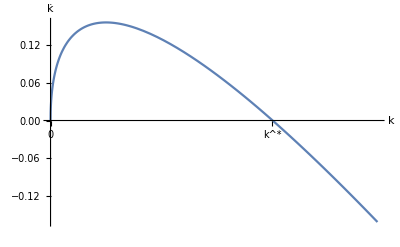

```mathematica
L=Plot[0.5*Sqrt[t]-0.4*t,{t,0,2.3},Ticks->{{{0,"0"},{1.56,"k^*"}},None},AxesLabel->{k,k̇},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"]]
```

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig1.pdf",L,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig1.pdf

```mathematica
"D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig1.pdf"
```

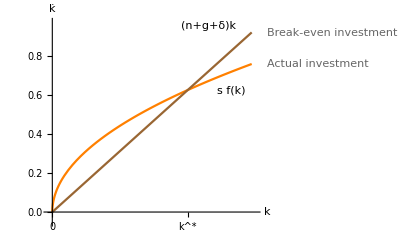

```mathematica
L2=Plot[{0.5*Sqrt[t],0.4*t},{t,0,2.3},Ticks->{{{0,"0"},{1.56,"k^*"}},None},AxesLabel->{k,k̇},AxesStyle->Directive[FontSize->13,FontFamily->"Times New Roman"],PlotLabels->{"Actual investment","Break-even investment"},PlotStyle->{Orange,Brown}]
```

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig2.pdf",L2,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig2.pdf